# Coëvolution of the genome Heuristic

Model

#### Full Model

```mathematica
Off[General::spell1]
Off[General::spell]
(*Modelling two species of replicator, that can replicate independently or in cross species pairs. Each species does better in the pairs due to byproduct benefits. We are interested in the evolution of costly cooperation in one species and the evolution of some kind of "stickiness" in the other species. That can take the form of increasing the probability of association or decreasing the probability of disassociation*)
(*
a = density of species a
b = density of species b
ab = density of ab complexes
fa = growth of a (ρa - μa)
fb = growth of b (ρb - μb)
ρa = birth of a alone (ra((1-(k(a[t]+b[t]+ab[t])))))
ρb = birth of b alone (rb((1-(k(a[t]+b[t]+ab[t])))))
ρab = birth of ab (rab((1-(k(a[t]+b[t]+ab[t])))))
k= density dependence
μa = death of a
μb = death of b 
θa = birth of a from complexes (1+κ)ρa
θb = birth of b from complexes (1+κ)ρb
κ = growth advantage to being in complex
β = association of a and b
δ = dissociation from a and b
c= amount of stickiness, 
					where 1-c is cost and 1+αc is increase in re-
					pairing from complexes, 			1+ζc is increase in association rate and 1-ξc is decrease in dissociation. 
				d= amount of cooperation, where 1-d is cost and 1+ λd is increase in repairing, and 1+ ωd is benefit to partner. 
*)

(* system of equations:
{a'[t]==((ρa-μa)a[t]) - (β a[t]b[t]) + ((μb + θa + δ)ab[t]),
b'[t]==((ρb-μb)b[t]) - (β a[t]b[t]) + ((μa + θb + δ)ab[t]),
ab'[t]==(β a[t]b[t]) - ((μa +μb + δ - ρab)ab[t]),
*)



t=.

NSolution[c_,α_,d_,ω_, λ_, χ_, υ_,ζ_,ξ_, ra_,rb_,rab_, k_, μa_, μb_,  κ_, β_, δ_,  astart_, bstart_, abstart_ ]:=

NDSolve[
{{a'[t]==(((ra(1-c)((1-k(a[t]+ab[t]+b[t]))))-μa)a[t]) - ((1+ζ c)β a[t] b[t]) + (((((1+κ)ra(1-c)(1+ ω d)((1-k(a[t]+ab[t]+b[t])))))+ μb + (1-ξ c)δ)ab[t]) ,
b'[t]==(((rb(1-d)((1-k(a[t]+ab[t]+b[t]))))-μb)b[t]) - ((1+ζ c)β a[t] b[t]) + ((((1+κ)(1-d)rb((1-k(a[t]+ab[t]+b[t])))) + μa+ (1-ξ c)δ)ab[t]),
ab'[t]==((1+ζ c)β  a[t] b[t]) - ((μa +μb + (1-ξ c)δ- ((1+λ d)(1+α c))rab((1-k(a[t]+ab[t]+b[t]))))ab[t])},
a[0]==astart,b[0]==bstart,ab[0]==abstart},{a,b,ab},{t,0,10000}];
```

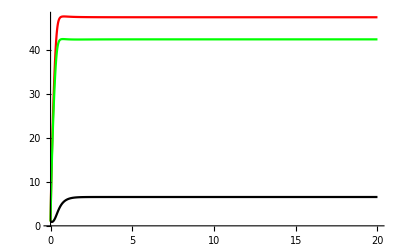

A :

{47.4221}

B :

{42.3976}

AB :

{6.55474}

```mathematica
(*visualising the ecological dynamics*)
param={c,α,d,ω, λ, χ,υ,ζ,ξ, ra,rb,rab, k,μa,μb,κ,β,δ,astart,bstart,abstart}//.{c->0,α->20, λ->20, d->0, ω->20,χ->10,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9, k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9,astart->1,bstart->1,abstart->1};

Plot[{a[time]/.NSolution@@param,
b[time]/.NSolution@@param,
ab[time]/.NSolution@@param},{time,0,20},PlotStyle->{Red,Green,Black},PlotRange->All]
Print["A : "];eqa=a[time]/.NSolution@@param/.time->100

Print["B : "];eqb=b[time]/.NSolution@@param/.time->100
Print["AB : "];eqab=ab[time]/.NSolution@@param/.time->100
```

Evolutionary Model

## Next Generation approach:

The idea is to start assume that the mutant is rare (which allows to linearize the dynamics of the mutant) and the the resident strategy has reached an endemic equilibrium (so that the sizes of the populations have reached some equilibrium). 
One can use a Next Generation Matrix to derive the per-generation invasion number Rm of the mutant host (see for instance).
When Rm>1 the mutant invades (note, however, that you need λm and H to obtain Rm).

```mathematica
(*When species A evolves*) 
FmA=({{Subscript[F, A], Subscript[P, A]}, {0, 0}}); (*reproduction*)
VmA=({{Subscript[β, A] Y, 0}, {-Subscript[β, A] Y, Subscript[M, AB]}}); (*transition between states*)


FmAVmA=FmA.Inverse[VmA]//MatrixForm
FmVmA=FmA-VmA//MatrixForm
```

(P_A/M_AB+F_A/(Y β_A) | P_A/M_AB
0 | 0)

(F_A-Y β_A | P_A
Y β_A | -M_AB)

```mathematica
(*We are looking for the dominant eigenvalue Rm of the per-generation transition matrix FmVm*)
EmA=Eigensystem[FmA.Inverse[VmA]]
RmA=FullSimplify[EmA[[1,2]]]


emA=Eigensystem[FmA-VmA];
rmA=FullSimplify[emA[[1,2]]];
```

{{0,(F_A M_AB+Y P_A β_A)/(Y M_AB β_A)},{{-(Y P_A β_A)/(F_A M_AB+Y P_A β_A),1},{1,0}}}

P_A/M_AB+F_A/(Y β_A)

```mathematica
Invasion of Stickiness in A
```

A in Invasion of Stickiness

```mathematica
(*invasion fitness of the STICKINESS mutant in species A *)
cm=.
Subscript[F, A]=((ra(1-cm)((1-k(a[t]+ab[t]+b[t]))))-μa);
Subscript[P, A]=(((((1+κ)ra(1-cm)(1+ ω d)((1-k(a[t]+ab[t]+b[t])))))+ μb + (1-ξ cm)δ));
Subscript[M, AB]=((μa +μb + (1-ξ cm)δ- ((1+λ d)(1+α cm))rab((1-k(a[t]+ab[t]+b[t])))));
Subscript[β, A]=(1+ζ cm)β ;
Subscript[Rm, A]=Subscript[P, A]/Subscript[M, AB]+Subscript[F, A]/(b[t] Subscript[β, A])
```

(-μa+(1-cm) ra (1-k (a[t]+ab[t]+b[t])))/(β (1+cm ζ) b[t])+(μb+δ (1-cm ξ)+(1-cm) ra (1+κ) (1+d ω) (1-k (a[t]+ab[t]+b[t])))/(μa+μb+δ (1-cm ξ)-rab (1+cm α) (1+d λ) (1-k (a[t]+ab[t]+b[t])))

```mathematica
(*Write invasion fitness in terms of parameter values *)

RmfunA[cm_,α_, d_,ω_,λ_, χ_,υ_,ζ_,ξ_, ra_,rb_,rab_, k_,μa_,μb_,κ_,β_,δ_]:=Evaluate[Subscript[Rm, A]]
gradRmfunA[cm_,α_, d_,ω_,λ_, χ_,υ_,ζ_,ξ_, ra_,rb_,k_,μa_,μb_,κ_,β_,δ_]:=Evaluate[D[Subscript[Rm, A],cm]/.cm->c]
```

```mathematica
RmfunA@@param1
```

param1

```mathematica
(*Confirm that neutral mutant (cm=c) won't evolve (Rm=1) *)
c=.;
cm=.;
param1={cm,α,d,ω,λ, χ,υ,ζ,ξ, ra,rb,rab,k,μa,μb,κ,β,δ}//.{cm->.5,α->20,d->0, ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1, ra->2.3,rb->2.1,rab->.9,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9};
param2={c,α,d,ω,λ, χ,υ,ζ,ξ, ra,rb,rab,k,μa,μb,κ,β,δ,astart,bstart,abstart}//.{c->.5,α->20,d->0, ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1, ra->2.3,rb->2.1,rab->.9,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9,astart->1,bstart->1,abstart->1};
RmfunA@@param1/.NSolution@@param2/.t->500
```

{1.}

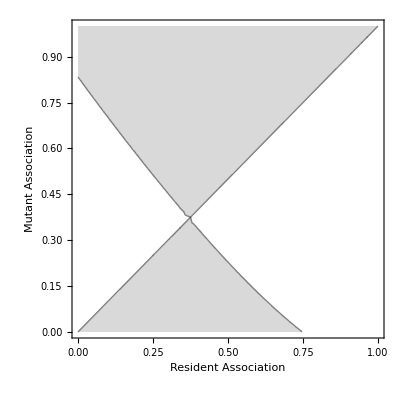

```mathematica
(*Contour plot of mutant trait values (Rm>1)*)
param3={cm,α,d,ω,λ, χ,υ,ζ,ξ, ra,rb,rab,k,μa,μb,κ,β,δ}//.{cm->cm,α->20,d->0, ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9};
param4={c,α,d,ω,λ, χ,υ,ζ,ξ,ra,rb,rab,k,μa,μb,κ,β,δ,astart,bstart,abstart}//.{c->c,α->20,d->0, ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9,astart->1,bstart->1,abstart->1};

ContourPlot[RmfunA@@param3/.NSolution@@param4/.t->500,{c,0,1},{cm,0,1},Contours->{1},ContourShading->{LightGray,White},FrameTicksStyle->Directive[FontFamily->"Helvetica", 12],FrameLabel->{Style["Resident Association ", Bold, 18], Style[ "Mutant Association", Bold, 18]},LabelStyle->Directive["Helvetica"]]
```

```mathematica
Invasion of Cooperation in B
```

B Cooperation in Invasion of

```mathematica
(*When species B evolves*) 
FmB=({{Subscript[F, B], Subscript[P, B]}, {0, 0}}); (*reproduction*)
VmB=({{Subscript[β, B] X, 0}, {-Subscript[β, B] X, Subscript[M, BA]}}); (*transition between states*)


FmBVmB=FmB.Inverse[VmB]//MatrixForm
FmBVmB=FmB-VmB//MatrixForm
```

(P_B/M_BA+F_B/(X β_B) | P_B/M_BA
0 | 0)

(F_B-X β_B | P_B
X β_B | -M_BA)

```mathematica
(*We are looking for the dominant eigenvalue Rm of the per-generation transition matrix FmVm*)
EmB=Eigensystem[FmB.Inverse[VmB]]
RmB=FullSimplify[EmB[[1,2]]]


emB=Eigensystem[FmB-VmB];
rmB=FullSimplify[emB[[1,2]]];
```

{{0,(F_B M_BA+X P_B β_B)/(X M_BA β_B)},{{-(X P_B β_B)/(F_B M_BA+X P_B β_B),1},{1,0}}}

P_B/M_BA+F_B/(X β_B)

```mathematica
(*invasion fitness of the COOPERATION mutant in species B *)
dm=.
Subscript[F, b]=((rb(1-dm)((1-k(a[t]+ab[t]+b[t]))))-μb);
Subscript[P, b]=((((1+κ)(1-dm)rb((1-k(a[t]+ab[t]+b[t])))) + μa+ (1-ξ c)δ)ab[t]);
Subscript[M, BA]=((μa +μb + (1-ξ c)δ- ((1+λ dm)(1+α c))rab((1-k(a[t]+ab[t]+b[t]))))ab[t]);
Subscript[β, b]=(1+ζ c)β ;
Subscript[Rm, B]=Subscript[P, b]/Subscript[M, BA]+Subscript[F, b]/(a[t] Subscript[β, b])
```

(-μb+(1-dm) rb (1-k (a[t]+ab[t]+b[t])))/(β (1+c ζ) a[t])+(μa+δ (1-c ξ)+(1-dm) rb (1+κ) (1-k (a[t]+ab[t]+b[t])))/(μa+μb+δ (1-c ξ)-rab (1+c α) (1+dm λ) (1-k (a[t]+ab[t]+b[t])))

```mathematica
(*Write invasion fitness in terms of parameter values *)
RmfunB[c_,α_, dm_,ω_,λ_,χ_,υ_,ζ_,ξ_, ra_,rb_,rab_,k_,μa_,μb_,κ_,β_,δ_]:=Evaluate[Subscript[Rm, B]]
gradRmfunB[c_,α_, dm_,ω_,λ_, χ_,υ_,ζ_,ξ_, ra_,rb_,rab_,k_,μa_,μb_,κ_,β_,δ_]:=Evaluate[D[Subscript[Rm, B],dm]/.dm->d]
```

```mathematica
(*Confirm that neutral mutant (cm=c) won't evolve (Rm=1) *)
d=.;
dm=.;
param5={c,α,dm,ω, λ, χ,υ,ζ,ξ, ra,rb,rab,k,μa,μb,κ,β,δ}//.{c->0,α->20,dm->0.5,ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9};
param6={c,α,d,ω,λ, χ,υ,ζ,ξ, ra,rb,rab,k,μa,μb,κ,β,δ,astart,bstart,abstart}//.{c->0,α->20,d->0.5,ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9,astart->1,bstart->1,abstart->1};
RmfunB@@param5/.NSolution@@param6/.t->500
```

{1.}

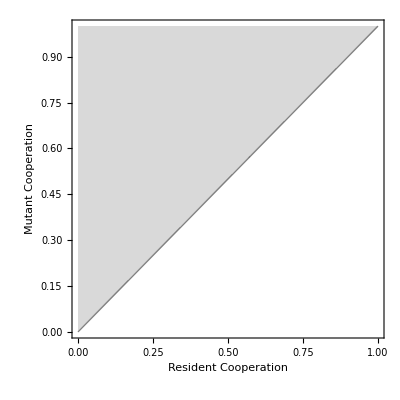

```mathematica
(*Contour plot of mutant trait values (Rm>1) before stickiness evolves (c=0)*)
param7={c,α,dm,ω, λ, χ,υ, ζ,ξ,ra,rb,rab, k,μa,μb,κ,β,δ}//.{c->0,α->20,dm->dm,ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9};
param8={c,α,d,ω,λ, χ,υ,ζ,ξ,ra,rb,rab,k,μa,μb,κ,β,δ,astart,bstart,abstart}//.{c->0,α->20,d->d,ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9,astart->1,bstart->1,abstart->1};

ContourPlot[RmfunB@@param7/.NSolution@@param8/.t->500,{d,0,1},{dm,0,1},Contours->{1},ContourShading->{LightGray,White},FrameTicksStyle->Directive[FontFamily->"Helvetica", 12],FrameLabel->{Style["Resident Cooperation ", Bold, 18], Style[ "Mutant Cooperation", Bold, 18]},LabelStyle->Directive["Helvetica"]]
```

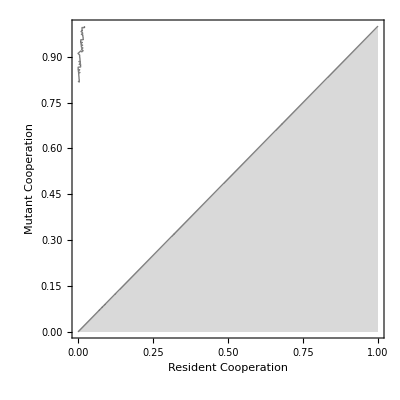

```mathematica
(*Contour plot of mutant trait values (Rm>1) after stickiness evolves (c=.4)*)
param9={c,α,dm,ω, λ, χ,υ,ζ,ξ, ra,rb,rab,k,μa,μb,κ,β,δ}//.{c->.4,α->20,dm->dm,ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9};
param10={c,α,d,ω,λ, χ,υ,ζ,ξ,ra,rb,rab,k,μa,μb,κ,β,δ,astart,bstart,abstart}//.{c->.4,α->20,d->d,ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9,astart->1,bstart->1,abstart->1};

ContourPlot[RmfunB@@param9/.NSolution@@param10/.t->500,{d,0,1},{dm,0,1},Contours->{1},ContourShading->{LightGray,White},FrameTicksStyle->Directive[FontFamily->"Helvetica", 12],FrameLabel->{Style["Resident Cooperation ", Bold, 18], Style[ "Mutant Cooperation", Bold, 18]},LabelStyle->Directive["Helvetica"]]
```

```mathematica
(*Pairwise invasibility plot looking at coevolution*)
gradRmfunA[cm_,α_, d_,ω_,λ_, χ_,υ_,ζ_,ξ_, ra_,rb_,rab_,k_,μa_,μb_,κ_,β_,δ_]:=Evaluate[D[Subscript[Rm, A],cm]/.cm->c]
gradRmfunB[c_,α_, dm_,ω_, λ_,χ_,υ_,ζ_,ξ_, ra_,rb_,rab_,k_,μa_,μb_,κ_,β_,δ_]:=Evaluate[D[Subscript[Rm, B],dm]/.dm->d]
```

```mathematica
R01=ContourPlot[R0[p/20,py/20,Fs,Fy,κ,b,β,m,δs,δy,a,α,nh,ϕ,τ],{p,1,19},{py,1,19},PlotRange->{{1,19},{1,19}},PlotPoints->80,Contours->{1},ContourShading->{Black,None},Frame->None];
```

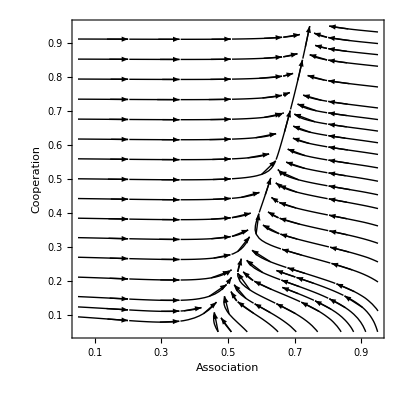

```mathematica
(*Coevolution*)
param={c,α,d,ω,λ, χ, υ,ζ,ξ,ra,rb,rab,k,μa,μb,κ,β,δ}//.{c->c,α->20,d->d,ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9};
paramEpid={c,α,d,ω,λ, χ,υ,ζ,ξ,ra,rb,rab,k,μa,μb,κ,β,δ,astart,bstart,abstart}//.{c->c,α->20,d->d,ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9,astart->1,bstart->1,abstart->1};


data=Table[{First [gradRmfunA@@param/.NSolution@@paramEpid/.t->500],First[gradRmfunB@@param/.NSolution@@paramEpid/.t->500]},{c,0.05,0.95,0.05},{d,0.05,0.95,0.05}];
gradPlot=ListStreamPlot[data,PlotTheme->"Monochrome",StreamPoints->50,StreamScale->{Large,All,0.04},PlotRange->All,Frame->True,ImageMargins->1,StreamStyle->"Arrow",FrameTicks->{{Table[{i,i*0.1/2},{i,2,18,2}],None},{Table[{i,i*0.1/2},{i,2,18,2}], None}},FrameLabel->{Style["Association", Bold,Gray, 18], Style[ "Cooperation", Bold,Gray, 18]},LabelStyle->Directive["Helvetica"], FrameTicksStyle->Directive[Black,10],AxesStyle->LightGray]
```

```mathematica
(*Potentially better code for pairwise plot*)
paramA={c,α,d,ω,λ, χ,υ,ζ,ξ, ra,rb,rab,k,μa,μb,κ,β,δ}//.{c->c, α->20,d-> d,ω->20,λ->20, χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9};
paramB={c,α,d,ω,λ, χ,υ,ζ,ξ, ra,rb,rab,k,μa,μb,κ,β,δ}//.{c->c, α->20,d-> d,ω->20,λ->20, χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9};
paramNum={c,α,d,ω,λ, χ,υ,ζ,ξ,ra,rb,rab,k,μa,μb,κ,β,δ,astart,bstart,abstart}//.{c->c,α->20,d->d,ω->20,λ->20, χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9,astart->1,bstart->1,abstart->1};
data=Table[{First [gradRmfunA@@paramA/.NSolution@@paramNum/.t->500],First[gradRmfunB@@paramB/.NSolution@@paramNum/.t->500]},{c,0.05,0.95,0.05},{d,0.05,0.95,0.05}];
gradPlot=ListStreamPlot[data,PlotTheme->"Monochrome",StreamPoints->50,StreamScale->{Large,All,0.04},PlotRange->All,Frame->True,ImageMargins->1,StreamStyle->"Arrow",FrameTicks->{{Table[{i,i*0.1/2},{i,2,18,2}],None},{Table[{i,i*0.1/2},{i,2,18,2}], None}},FrameLabel->{Style["Association", Bold,Gray, 18], Style[ "Cooperation", Bold,Gray, 18]},LabelStyle->Directive["Helvetica"], FrameTicksStyle->Directive[Black,10],AxesStyle->LightGray]
```

-Graphics-

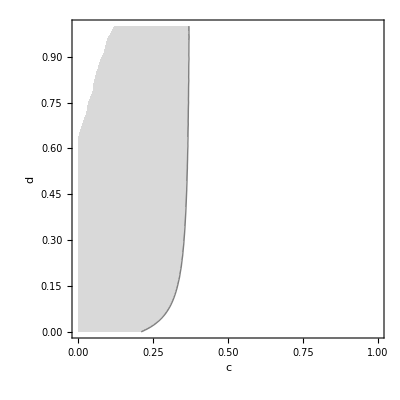

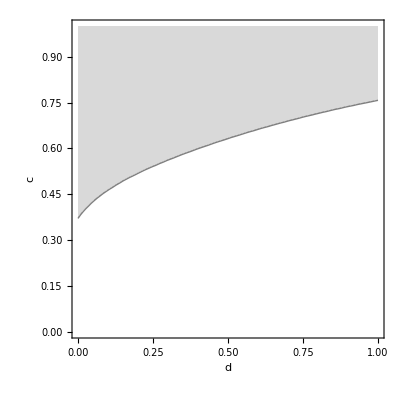

```mathematica
(*Looking at ESS's*)
gradRmfunA2[cm_,α_, d_,ω_,λ_, χ_,υ_,ζ_,ξ_, ra_,rb_,rab_,k_,μa_,μb_,κ_,β_,δ_]:=Evaluate[D[Subscript[Rm, A],cm]/.cm->c]
gradRmfunB2[c_,α_, dm_,ω_, λ_,χ_,υ_,ζ_,ξ_, ra_,rb_,rab_,k_,μa_,μb_,κ_,β_,δ_]:=Evaluate[D[Subscript[Rm, B],dm]/.dm->d]
parama11={c,α,d,ω,λ, χ,υ, ζ,ξ,ra,rb,rab,k,μa,μb,κ,β,δ}//.{c->c,α->20,d->d,ω->20,λ->20, χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9};
paramEpid11={c,α,d,ω,λ, χ,υ,ζ,ξ,ra,rb,rab,k,μa,μb,κ,β,δ,astart,bstart,abstart}//.{c->c,α->20,d->d,ω->20,λ->20, χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9,astart->1,bstart->1,abstart->1};
ContourPlot[gradRmfunB2@@parama11/.NSolution@@paramEpid11/.t->500,{c,0,1},{d,0,1},Contours->{0},ContourShading->{LightGray,White}, AxesLabel->Automatic]
ContourPlot[gradRmfunA2@@parama11/.NSolution@@paramEpid11/.t->500,{d,0,1},{c,0,1},Contours->{0},ContourShading->{LightGray,White}, AxesLabel->Automatic]
```

# Coëvolution of the genome Same Type Pairs

Model

#### Full Model

```mathematica
Off[General::spell1]
Off[General::spell]
(*Modelling two species of replicator, that can replicate independently or in cross species pairs. Each species does better in the pairs due to byproduct benefits. We are interested in the evolution of costly cooperation in one species and the evolution of some kind of "stickiness" in the other species. That can take the form of increasing the probability of association or decreasing the probability of disassociation*)
(*
a = density of species a
b = density of species b
ab = density of ab complexes
fa = growth of a (ρa - μa)
fb = growth of b (ρb - μb)
ρa = birth of a alone (ra((1-(k(a[t]+b[t]+ab[t])))))
ρb = birth of b alone (rb((1-(k(a[t]+b[t]+ab[t])))))
ρab = birth of ab (rab((1-(k(a[t]+b[t]+ab[t])))))
k= density dependence
μa = death of a
μb = death of b 
θa = birth of a from complexes (1+κ)ρa
θb = birth of b from complexes (1+κ)ρb
κ = growth advantage to being in complex
β = association of a and b
δ = dissociation from a and b
c= amount of stickiness, 
					where 1-c is cost and 1+αc is increase in re-
					pairing from complexes, 			1+ζc is increase in association rate and 1-ξc is decrease in dissociation. 
				d= amount of cooperation, where 1-d is cost and 1+ λd is increase in repairing, and 1+ ωd is benefit to partner. 
*)

(* system of equations:
{a'[t]==((ρa-μa)a[t]) - (β a[t]b[t]) + ((μb + θa + δ)ab[t]),
b'[t]==((ρb-μb)b[t]) - (β a[t]b[t]) + ((μa + θb + δ)ab[t]),
ab'[t]==(β a[t]b[t]) - ((μa +μb + δ - ρab)ab[t]),
*)



t=.

NSolution[c_,α_,d_,ω_, λ_, χ_, υ_,ζ_,ξ_, ra_,rb_,rab_, raa_,rbb_, k_, μa_, μb_,  κ_, β_, δ_,  astart_, bstart_, abstart_ , aastart_, bbstart_]:=

NDSolve[
{{a'[t]==(((ra(1-c)((1-k(a[t]+ab[t]+b[t]+aa[t]+bb[t]))))-μa)a[t]) - ((1+ζ c)β a[t] b[t]) -(β  a[t] a[t])+ (((((1+κ)ra(1-c)(1+ ω d)((1-k(a[t]+ab[t]+b[t]+aa[t]+bb[t])))))+ μb + (1-ξ c)δ)ab[t])+ ((μa + δ + ra(1-c)((1-k(a[t]+ab[t]+b[t]+aa[t]+bb[t])))))aa[t] ,
b'[t]==(((rb(1-d)((1-k(a[t]+ab[t]+b[t]+aa[t]+bb[t]))))-μb)b[t]) - ((1+ζ c)β a[t] b[t])-(β  b[t] b[t]) + ((((1+κ)(1-d)rb((1-k(a[t]+ab[t]+b[t]+aa[t]+bb[t])))) + μa+ (1-ξ c)δ)ab[t])+ ((μb +δ + rb(1-d)((1-k(a[t]+ab[t]+b[t]+aa[t]+bb[t])))))bb[t],
ab'[t]==((1+ζ c)β  a[t] b[t]) - ((μa +μb + (1-ξ c)δ- ((1+λ d)(1+α c))rab((1-k(a[t]+ab[t]+b[t]+aa[t]+bb[t]))))ab[t]),
aa'[t] == (β  a[t] a[t])- ((μa +μa + δ - raa((1-k(a[t]+ab[t]+b[t]+aa[t]+bb[t])))))aa[t],
bb'[t]== (β  b[t] b[t])- ((μb +μb +δ - rbb((1-k(a[t]+ab[t]+b[t]+aa[t]+bb[t])))))bb[t]},
a[0]==astart,b[0]==bstart,ab[0]==abstart, aa[0]== aastart, bb[0]==bbstart},{a,b,ab, aa, bb},{t,0,10000}];
```

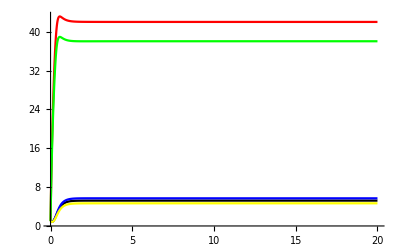

A :

{42.0068}

B :

{38.0293}

AB :

{5.21967}

AA :

{5.69217}

BB :

{4.66525}

```mathematica
(*visualising the ecological dynamics*)
param={c,α,d,ω, λ, χ,υ,ζ,ξ, ra,rb,rab,raa, rbb, k,μa,μb,κ,β,δ,astart,bstart,abstart, aastart, bbstart}//.{c->0,α->20, λ->20, d->0, ω->20,χ->10,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,raa->0, rbb->0, k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9,astart->1,bstart->1,abstart->1 , aastart->1, bbstart->1};

Plot[{a[time]/.NSolution@@param,
b[time]/.NSolution@@param,
ab[time]/.NSolution@@param,
aa[time]/. NSolution@@param,
bb[time] /. NSolution@@param},{time,0,20},PlotStyle->{Red,Green,Black, Blue, Yellow},PlotRange->All]
Print["A : "];eqa=a[time]/.NSolution@@param/.time->100

Print["B : "];eqb=b[time]/.NSolution@@param/.time->100
Print["AB : "];eqab=ab[time]/.NSolution@@param/.time->100
Print["AA : "];eqaa=aa[time]/.NSolution@@param/.time->100
Print["BB : "];eqbb=bb[time]/.NSolution@@param/.time->100
```

Evolutionary Model

## Next Generation approach:

The idea is to start assume that the mutant is rare (which allows to linearize the dynamics of the mutant) and the the resident strategy has reached an endemic equilibrium (so that the sizes of the populations have reached some equilibrium). 
One can use a Next Generation Matrix to derive the per-generation invasion number Rm of the mutant host (see for instance).
When Rm>1 the mutant invades (note, however, that you need λm and H to obtain Rm).

```mathematica
(*When species A evolves*) 
FmA=({{Subscript[F, A], Subscript[P, A], Subscript[P, AA]}, {0, 0, 0}, {0, 0, 0}}); (*reproduction*)
VmA=({{Subscript[β, A] Y +β X, 0, 0}, {-Subscript[β, A] Y, Subscript[M, AB], 0}, {-β X, 0, Subscript[M, AA]}}); (*transition between states*)
(* checking that next gen approach is valid *)
Eigenvalues[-VmA]
Inverse[VmA]

FmAVmA=FmA.Inverse[VmA]//MatrixForm
FmVmA=FmA-VmA//MatrixForm
```

{-M_AA,-M_AB,-X β-Y β_A}

{{(M_AA M_AB)/(X β M_AA M_AB+Y M_AA M_AB β_A),0,0},{(Y M_AA β_A)/(X β M_AA M_AB+Y M_AA M_AB β_A),(X β M_AA+Y M_AA β_A)/(X β M_AA M_AB+Y M_AA M_AB β_A),0},{(X β M_AB)/(X β M_AA M_AB+Y M_AA M_AB β_A),0,(X β M_AB+Y M_AB β_A)/(X β M_AA M_AB+Y M_AA M_AB β_A)}}

((F_A M_AA M_AB)/(X β M_AA M_AB+Y M_AA M_AB β_A)+(X β M_AB P_AA)/(X β M_AA M_AB+Y M_AA M_AB β_A)+(Y M_AA P_A β_A)/(X β M_AA M_AB+Y M_AA M_AB β_A) | (P_A (X β M_AA+Y M_AA β_A))/(X β M_AA M_AB+Y M_AA M_AB β_A) | (P_AA (X β M_AB+Y M_AB β_A))/(X β M_AA M_AB+Y M_AA M_AB β_A)
0 | 0 | 0
0 | 0 | 0)

(-X β+F_A-Y β_A | P_A | P_AA
Y β_A | -M_AB | 0
X β | 0 | -M_AA)

```mathematica
(*We are looking for the dominant eigenvalue Rm of the per-generation transition matrix FmVm*)
EmA=Eigensystem[FmA.Inverse[VmA]]
RmA=FullSimplify[EmA[[1,3]]]


emA=Eigensystem[FmA-VmA];
rmA=FullSimplify[emA[[1,3]]];
```

{{0,0,(F_A M_AA M_AB+X β M_AB P_AA+Y M_AA P_A β_A)/(M_AA M_AB (X β+Y β_A))},{{-(M_AB P_AA (X β+Y β_A))/(F_A M_AA M_AB+X β M_AB P_AA+Y M_AA P_A β_A),0,1},{-(M_AA P_A (X β+Y β_A))/(F_A M_AA M_AB+X β M_AB P_AA+Y M_AA P_A β_A),1,0},{1,0,0}}}

(M_AB (F_A M_AA+X β P_AA)+Y M_AA P_A β_A)/(M_AA M_AB (X β+Y β_A))

```mathematica
Invasion of Stickiness in A
```

A in Invasion of Stickiness

```mathematica
(*invasion fitness of the STICKINESS mutant in species A *)
cm=.
Subscript[F, A]=((ra(1-cm)((1-k(a[t]+ab[t]+b[t]+aa[t]+bb[t]))))-μa);
Subscript[P, A]=(((((1+κ)ra(1-cm)(1+ ω d)((1-k(a[t]+ab[t]+b[t]+aa[t]+bb[t])))))+ μb + (1-ξ cm)δ));
Subscript[M, AB]=((μa +μb + (1-ξ cm)δ- ((1+λ d)(1+α cm))rab((1-k(a[t]+ab[t]+b[t]+aa[t]+bb[t])))));
Subscript[β, A]=(1+ζ cm)β ;
Subscript[P, AA]= (μa + δ + ra(1-cm)((1-k(a[t]+ab[t]+b[t]+aa[t]+bb[t]))));
Subscript[M, AA]= ((μa +μa + δ - raa((1-k(a[t]+ab[t]+b[t]+aa[t]+bb[t])))));
Subscript[Rm, A]=(Subscript[M, AB] (Subscript[F, A] Subscript[M, AA]+a[t] β Subscript[P, AA])+b[t] Subscript[M, AA] Subscript[P, A] Subscript[β, A])/(Subscript[M, AA] Subscript[M, AB] (a[t] β+b[t] Subscript[β, A]))
```

(β (1+cm ζ) b[t] (δ+2 μa-raa (1-k (a[t]+aa[t]+ab[t]+b[t]+bb[t]))) (μb+δ (1-cm ξ)+(1-cm) ra (1+κ) (1+d ω) (1-k (a[t]+aa[t]+ab[t]+b[t]+bb[t])))+(μa+μb+δ (1-cm ξ)-rab (1+cm α) (1+d λ) (1-k (a[t]+aa[t]+ab[t]+b[t]+bb[t]))) (β a[t] (δ+μa+(1-cm) ra (1-k (a[t]+aa[t]+ab[t]+b[t]+bb[t])))+(-μa+(1-cm) ra (1-k (a[t]+aa[t]+ab[t]+b[t]+bb[t]))) (δ+2 μa-raa (1-k (a[t]+aa[t]+ab[t]+b[t]+bb[t])))))/((β a[t]+β (1+cm ζ) b[t]) (δ+2 μa-raa (1-k (a[t]+aa[t]+ab[t]+b[t]+bb[t]))) (μa+μb+δ (1-cm ξ)-rab (1+cm α) (1+d λ) (1-k (a[t]+aa[t]+ab[t]+b[t]+bb[t]))))

```mathematica
(*Write invasion fitness in terms of parameter values *)

RmfunA[cm_,α_, d_,ω_,λ_, χ_,υ_,ζ_,ξ_, ra_,rb_,rab_,raa_,rbb_, k_,μa_,μb_,κ_,β_,δ_]:=Evaluate[Subscript[Rm, A]]
gradRmfunA[cm_,α_, d_,ω_,λ_, χ_,υ_,ζ_,ξ_, ra_,rb_,rab_,raa_, rbb_,k_,μa_,μb_,κ_,β_,δ_]:=Evaluate[D[Subscript[Rm, A],cm]/.cm->c]
```

```mathematica
RmfunA@@param1
```

param1

```mathematica
(*Confirm that neutral mutant (cm=c) won't evolve (Rm=1) *)
c=.;
cm=.;
param1={cm,α,d,ω,λ, χ,υ,ζ,ξ, ra,rb,rab,raa, rbb, k,μa,μb,κ,β,δ}//.{cm->.5,α->20,d->0, ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1, ra->2.3,rb->2.1,rab->.9,raa->0, rbb->0,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9};
param2={c,α,d,ω,λ, χ,υ,ζ,ξ, ra,rb,rab, raa, rbb,k,μa,μb,κ,β,δ,astart,bstart,abstart, aastart, bbstart}//.{c->.5,α->20,d->0, ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1, ra->2.3,rb->2.1,rab->.9,raa->0, rbb->0,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9,astart->1,bstart->1,abstart->1, aastart->1, bbstart->1};
RmfunA@@param1/.NSolution@@param2/.t->500
```

{1.}

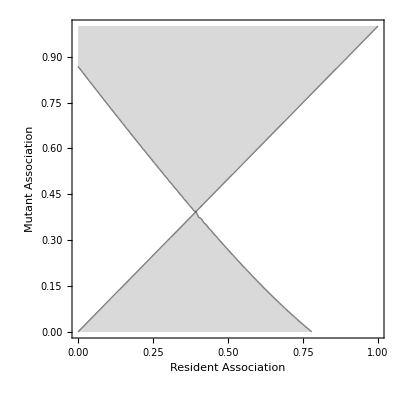

```mathematica
(*Contour plot of mutant trait values (Rm>1)*)
param3={cm,α,d,ω,λ, χ,υ,ζ,ξ, ra,rb,rab,raa, rbb, k,μa,μb,κ,β,δ}//.{cm->cm,α->20,d->0, ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,raa->0, rbb->0,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9};
param4={c,α,d,ω,λ, χ,υ,ζ,ξ,ra,rb,rab,raa, rbb,k,μa,μb,κ,β,δ,astart,bstart,abstart, aastart, bbstart}//.{c->c,α->20,d->0, ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,raa->0, rbb->0,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9,astart->1,bstart->1,abstart->1, aastart->1, bbstart->1};

ContourPlot[RmfunA@@param3/.NSolution@@param4/.t->500,{c,0,1},{cm,0,1},Contours->{1},ContourShading->{LightGray,White},FrameTicksStyle->Directive[FontFamily->"Helvetica", 12],FrameLabel->{Style["Resident Association ", Bold, 18], Style[ "Mutant Association", Bold, 18]},LabelStyle->Directive["Helvetica"]]
```

```mathematica
Invasion of Cooperation in B
```

B Cooperation in Invasion of

```mathematica
(*When species B evolves*) 
FmB=({{Subscript[F, B], Subscript[P, B], Subscript[P, BB]}, {0, 0, 0}, {0, 0, 0}}); (*reproduction*)
VmB=({{Subscript[β, B] X +β Y, 0, 0}, {-Subscript[β, B] X, Subscript[M, BA], 0}, {-β Y, 0, Subscript[M, BB]}}); (*transition between states*)

(* checking that next gen approach is valid *)
Eigenvalues[-VmB]
Inverse[VmB]

FmBVmB=FmB.Inverse[VmB]//MatrixForm
FmBVmB=FmB-VmB//MatrixForm
```

{-M_BA,-M_BB,-Y β-X β_B}

{{(M_BA M_BB)/(Y β M_BA M_BB+X M_BA M_BB β_B),0,0},{(X M_BB β_B)/(Y β M_BA M_BB+X M_BA M_BB β_B),(Y β M_BB+X M_BB β_B)/(Y β M_BA M_BB+X M_BA M_BB β_B),0},{(Y β M_BA)/(Y β M_BA M_BB+X M_BA M_BB β_B),0,(Y β M_BA+X M_BA β_B)/(Y β M_BA M_BB+X M_BA M_BB β_B)}}

((F_B M_BA M_BB)/(Y β M_BA M_BB+X M_BA M_BB β_B)+(Y β M_BA P_BB)/(Y β M_BA M_BB+X M_BA M_BB β_B)+(X M_BB P_B β_B)/(Y β M_BA M_BB+X M_BA M_BB β_B) | (P_B (Y β M_BB+X M_BB β_B))/(Y β M_BA M_BB+X M_BA M_BB β_B) | (P_BB (Y β M_BA+X M_BA β_B))/(Y β M_BA M_BB+X M_BA M_BB β_B)
0 | 0 | 0
0 | 0 | 0)

(-Y β+F_B-X β_B | P_B | P_BB
X β_B | -M_BA | 0
Y β | 0 | -M_BB)

```mathematica
(*We are looking for the dominant eigenvalue Rm of the per-generation transition matrix FmVm*)
EmB=Eigensystem[FmB.Inverse[VmB]]
RmB=FullSimplify[EmB[[1,3]]]


emB=Eigensystem[FmB-VmB];
rmB=FullSimplify[emB[[1,3]]];
```

{{0,0,(F_B M_BA M_BB+Y β M_BA P_BB+X M_BB P_B β_B)/(M_BA M_BB (Y β+X β_B))},{{-(M_BA P_BB (Y β+X β_B))/(F_B M_BA M_BB+Y β M_BA P_BB+X M_BB P_B β_B),0,1},{-(M_BB P_B (Y β+X β_B))/(F_B M_BA M_BB+Y β M_BA P_BB+X M_BB P_B β_B),1,0},{1,0,0}}}

(M_BA (F_B M_BB+Y β P_BB)+X M_BB P_B β_B)/(M_BA M_BB (Y β+X β_B))

```mathematica
(*invasion fitness of the COOPERATION mutant in species B *)
dm=.
Subscript[F, B]=((rb(1-dm)((1-k(a[t]+ab[t]+b[t]+aa[t]+bb[t]))))-μb);
Subscript[P, B]=((((1+κ)(1-dm)rb((1-k(a[t]+ab[t]+b[t]+aa[t]+bb[t])))) + μa+ (1-ξ c)δ)ab[t]);
Subscript[M, BA]=((μa +μb + (1-ξ c)δ- ((1+λ dm)(1+α c))rab((1-k(a[t]+ab[t]+b[t]+aa[t]+bb[t]))))ab[t]);
Subscript[β, B]=(1+ζ c)β ;
Subscript[P, BB]= (μb +δ + rb(1-dm)((1-k(a[t]+ab[t]+b[t]+aa[t]+bb[t]))));
Subscript[M, BB]= ((μb +μb +δ - rbb((1-k(a[t]+ab[t]+b[t]+aa[t]+bb[t])))));
Subscript[Rm, B]=(Subscript[M, BA] (Subscript[F, B] Subscript[M, BB]+b[t] β Subscript[P, BB])+a[t] Subscript[M, BB] Subscript[P, B] Subscript[β, B])/(Subscript[M, BA] Subscript[M, BB] (b[t] β+a[t] Subscript[β, B]))
```

(β (1+c ζ) a[t] ab[t] (δ+2 μb-rbb (1-k (a[t]+aa[t]+ab[t]+b[t]+bb[t]))) (μa+δ (1-c ξ)+(1-dm) rb (1+κ) (1-k (a[t]+aa[t]+ab[t]+b[t]+bb[t])))+ab[t] (μa+μb+δ (1-c ξ)-rab (1+c α) (1+dm λ) (1-k (a[t]+aa[t]+ab[t]+b[t]+bb[t]))) (β b[t] (δ+μb+(1-dm) rb (1-k (a[t]+aa[t]+ab[t]+b[t]+bb[t])))+(-μb+(1-dm) rb (1-k (a[t]+aa[t]+ab[t]+b[t]+bb[t]))) (δ+2 μb-rbb (1-k (a[t]+aa[t]+ab[t]+b[t]+bb[t])))))/(ab[t] (β (1+c ζ) a[t]+β b[t]) (δ+2 μb-rbb (1-k (a[t]+aa[t]+ab[t]+b[t]+bb[t]))) (μa+μb+δ (1-c ξ)-rab (1+c α) (1+dm λ) (1-k (a[t]+aa[t]+ab[t]+b[t]+bb[t]))))

```mathematica
(*Write invasion fitness in terms of parameter values *)
RmfunB[c_,α_, dm_,ω_,λ_,χ_,υ_,ζ_,ξ_, ra_,rb_,rab_,raa_, rbb_,k_,μa_,μb_,κ_,β_,δ_]:=Evaluate[Subscript[Rm, B]]
gradRmfunB[c_,α_, dm_,ω_,λ_, χ_,υ_,ζ_,ξ_, ra_,rb_,rab_,raa_, rbb_,k_,μa_,μb_,κ_,β_,δ_]:=Evaluate[D[Subscript[Rm, B],dm]/.dm->d]
```

```mathematica
(*Confirm that neutral mutant (cm=c) won't evolve (Rm=1) *)
d=.;
dm=.;
param5={c,α,dm,ω, λ, χ,υ,ζ,ξ, ra,rb,rab,raa, rbb,k,μa,μb,κ,β,δ}//.{c->0,α->20,dm->0.5,ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,raa->0, rbb->0,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9};
param6={c,α,d,ω,λ, χ,υ,ζ,ξ, ra,rb,rab,raa, rbb, k,μa,μb,κ,β,δ,astart,bstart,abstart, aastart, bbstart}//.{c->0,α->20,d->0.5,ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,raa->0, rbb->0,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9,astart->1,bstart->1,abstart->1, aastart->1, bbstart->1};
RmfunB@@param5/.NSolution@@param6/.t->500
```

{1.}

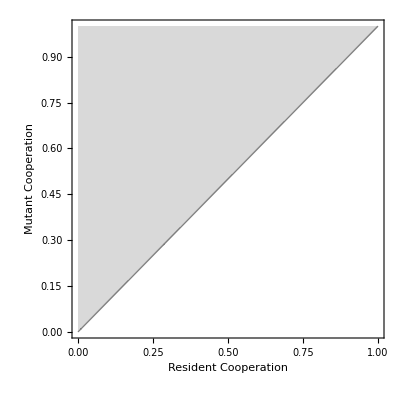

```mathematica
(*Contour plot of mutant trait values (Rm>1) before stickiness evolves (c=0)*)
param7={c,α,dm,ω, λ, χ,υ, ζ,ξ,ra,rb,rab,raa, rbb, k,μa,μb,κ,β,δ}//.{c->0,α->20,dm->dm,ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,raa->0, rbb->0,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9};
param8={c,α,d,ω,λ, χ,υ,ζ,ξ,ra,rb,rab,raa, rbb, k,μa,μb,κ,β,δ,astart,bstart,abstart, aastart, bbstart}//.{c->0,α->20,d->d,ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,raa->0, rbb->0,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9,astart->1,bstart->1,abstart->1, aastart->1, bbstart->1};

ContourPlot[RmfunB@@param7/.NSolution@@param8/.t->500,{d,0,1},{dm,0,1},Contours->{1},ContourShading->{LightGray,White},FrameTicksStyle->Directive[FontFamily->"Helvetica", 12],FrameLabel->{Style["Resident Cooperation ", Bold, 18], Style[ "Mutant Cooperation", Bold, 18]},LabelStyle->Directive["Helvetica"]]
```

```mathematica
(*Pairwise invasibility plot looking at coevolution*)
gradRmfunA[cm_,α_, d_,ω_,λ_, χ_,υ_,ζ_,ξ_, ra_,rb_,rab_,raa_, rbb_,k_,μa_,μb_,κ_,β_,δ_]:=Evaluate[D[Subscript[Rm, A],cm]/.cm->c]
gradRmfunB[c_,α_, dm_,ω_, λ_,χ_,υ_,ζ_,ξ_, ra_,rb_,rab_,raa_, rbb_,k_,μa_,μb_,κ_,β_,δ_]:=Evaluate[D[Subscript[Rm, B],dm]/.dm->d]
```

```mathematica
R01=ContourPlot[R0[p/20,py/20,Fs,Fy,κ,b,β,m,δs,δy,a,α,nh,ϕ,τ],{p,1,19},{py,1,19},PlotRange->{{1,19},{1,19}},PlotPoints->80,Contours->{1},ContourShading->{Black,None},Frame->None];
```

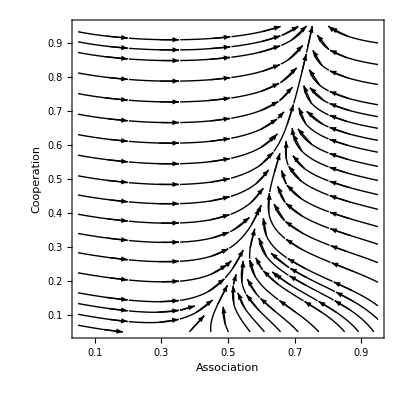

```mathematica
(*Coevolution when alpha is high*)
param={c,α,d,ω,λ, χ, υ,ζ,ξ,ra,rb,rab,raa, rbb, k,μa,μb,κ,β,δ}//.{c->c,α->20,d->d,ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,raa->0, rbb->0,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9};
paramEpid={c,α,d,ω,λ, χ,υ,ζ,ξ,ra,rb,rab,raa, rbb, k,μa,μb,κ,β,δ,astart,bstart,abstart, aastart, bbstart}//.{c->c,α->20,d->d,ω->20,λ->20,χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,raa->0, rbb->0,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9,astart->1,bstart->1,abstart->1, aastart->1, bbstart->1};


data=Table[{First [gradRmfunA@@param/.NSolution@@paramEpid/.t->500],First[gradRmfunB@@param/.NSolution@@paramEpid/.t->500]},{c,0.05,0.95,0.05},{d,0.05,0.95,0.05}];
gradPlot=ListStreamPlot[data,PlotTheme->"Monochrome",StreamPoints->50,StreamScale->{Large,All,0.04},PlotRange->All,Frame->True,ImageMargins->1,StreamStyle->"Arrow",FrameTicks->{{Table[{i,i*0.1/2},{i,2,18,2}],None},{Table[{i,i*0.1/2},{i,2,18,2}], None}},FrameLabel->{Style["Association", Bold,Gray, 18], Style[ "Cooperation", Bold,Gray, 18]},LabelStyle->Directive["Helvetica"], FrameTicksStyle->Directive[Black,10],AxesStyle->LightGray]
```

```mathematica
(*Potentially better code for pairwise plot*)
paramA={c,α,d,ω,λ, χ,υ,ζ,ξ, ra,rb,rab,raa, rbb, k,μa,μb,κ,β,δ}//.{c->c, α->20,d-> d,ω->20,λ->20, χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,raa->0, rbb->0,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9};
paramB={c,α,d,ω,λ, χ,υ,ζ,ξ, ra,rb,rab,raa, rbb, k,μa,μb,κ,β,δ}//.{c->c, α->20,d-> d,ω->20,λ->20, χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,raa->0, rbb->0,k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9};
paramNum={c,α,d,ω,λ, χ,υ,ζ,ξ,ra,rb,rab,raa, rbb, k,μa,μb,κ,β,δ,astart,bstart,abstart, aastart, bbstart}//.{c->c,α->20,d->d,ω->20,λ->20, χ->30,υ->.1,ζ->5, ξ->1,ra->2.3,rb->2.1,rab->.9,raa->0, rbb->0, k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,δ->.9,astart->1,bstart->1,abstart->1, aastart->1, bbstart->1};
data=Table[{First [gradRmfunA@@paramA/.NSolution@@paramNum/.t->500],First[gradRmfunB@@paramB/.NSolution@@paramNum/.t->500]},{c,0.05,0.95,0.05},{d,0.05,0.95,0.05}];
gradPlot=ListStreamPlot[data,PlotTheme->"Monochrome",StreamPoints->50,StreamScale->{Large,All,0.04},PlotRange->All,Frame->True,ImageMargins->1,StreamStyle->"Arrow",FrameTicks->{{Table[{i,i*0.1/2},{i,2,18,2}],None},{Table[{i,i*0.1/2},{i,2,18,2}], None}},FrameLabel->{Style["Association", Bold,Gray, 18], Style[ "Cooperation", Bold,Gray, 18]},LabelStyle->Directive["Helvetica"], FrameTicksStyle->Directive[Black,10],AxesStyle->LightGray]
```

-Graphics-

# Coëvolution mechanistic tracking

## Model

```mathematica
Off[General::spell1]
Off[General::spell]
(*Modelling two species of replicator, that can replicate independently or in cross species pairs. Each species does better in the pairs due to byproduct benefits. We are interested in the evolution of costly cooperation in one species and the evolution of some kind of "stickiness" in the other species. That can take the form of increasing the probability of association or decreasing the probability of disassociation*)
(*
a = density of species a
b = density of species b
ab = density of ab complexes
fa = growth of a (ρa - μa)
fb = growth of b (ρb - μb)
ρa = birth of a alone (ra((1-(k(a[t]+b[t]+ab[t])))))
ρb = birth of b alone (rb((1-(k(a[t]+b[t]+ab[t])))))
ρab = birth of ab (rab((1-(k(a[t]+b[t]+ab[t])))))
k= density dependence
μa = death of a
μb = death of b 
θa = birth of a from complexes (1+κ)ρa
θb = birth of b from complexes (1+κ)ρb
κ = growth advantage to being in complex
β = association of a and b
χ =re-association of produced a and b
δ = dissociation from a and b
c= amount of stickiness, 
					where 1-c is cost and
 				1+ζc is increase in association rate and 1-
					ξc is decrease in dissociation, 
						and (1+ψ c) is the increase in re-association rate
				d= amount of cooperation, 
					where 1-d is cost , 
						and 1+ ωd is benefit to partner. 
*)

(* system of equations:
{a'[t]==((ρa-μa)a[t]) - (β a[t]b[t]) + ((μb + δ)ab[t]) + a2[t],
b'[t]==((ρb-μb)b[t]) - (β a[t]b[t]) + ((μa + δ)ab[t]) + b2[t],
ab'[t]==(β a[t]b[t]) - ((μa +μb + δ)ab[t]) + (association)a2[t]b2[t],
a2'[t]== (production)ab[t] - (association)a2[t]b2[t],
b2'[t]== (production)ab[t] - (association)a2[t]b2[t],
*)



t=.

NSolution[c_,d_,ω_,λ_,α_, ζ_,ξ_, ψ_,ra_,rb_, k_, μa_, μb_,  κ_, β_,χ_, δ_,  astart_, bstart_, abstart_ , aOstart_, bOstart_]:=

NDSolve[
{{a'[t]==(((ra(1-c)((1-k(a[t]+ab[t]+b[t]+aO[t]+bO[t]))))-μa)a[t]) - ((1+ζ c)β a[t] b[t]) + (( μb + (1-ξ c)δ)ab[t]) +aO[t] ,
b'[t]==(((rb(1-d)((1-k(a[t]+ab[t]+b[t]+aO[t]+bO[t]))))-μb)b[t]) - ((1+ζ c)β a[t] b[t]) + (( μa+ (1-ξ c)δ)ab[t])+bO[t],
ab'[t]==((1+ζ c)β  a[t] b[t]) - ((μa +μb + (1-ξ c)δ)ab[t]) +((1+ψ c )(1+λ d)χ)aO[t] bO[t] ,aO'[t]== ((1+κ)ra(1-c)(1+ (1+α c)ω d)((1-k(a[t]+ab[t]+b[t]+aO[t]+bO[t]))))ab[t]-((1+ψ c )(1+λ d)χ)aO[t] bO[t]-aO[t] , bO'[t]== ((1+κ)(1-d)rb((1-k(a[t]+ab[t]+b[t]+aO[t]+bO[t]))))ab[t]-((1+ψ c )(1+λ d)χ)aO[t] bO[t]-bO[t]},
a[0]==astart,b[0]==bstart,ab[0]==abstart, aO[0]==aOstart, bO[0]==bOstart},{a,b,ab, aO, bO},{t,0,10000}];
```

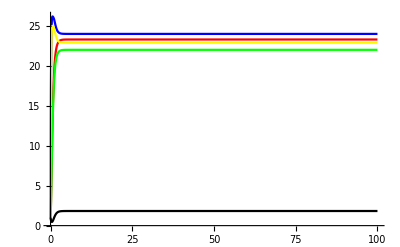

A :

{23.2852}

B :

{21.9949}

AB :

{1.82905}

AO :

{23.9848}

BO :

{22.8696}

```mathematica
(*visualising the ecological dynamics*)
param={c,d,ω,λ,α, ζ,ξ, ψ, ra,rb, k,μa,μb,κ,β,χ, δ,astart,bstart,abstart, aOstart, bOstart}//.{c->0, d->0, ω->10,λ->10,α->0,ζ->5, ξ->1,ψ-> 20, ra->2.2,rb->2.1, k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,χ->0.001, δ->.9,astart->1,bstart->1,abstart->1, aOstart->1, bOstart->1};

Plot[{a[time]/.NSolution@@param,
b[time]/.NSolution@@param,
ab[time]/.NSolution@@param,
aO[time]/. NSolution@@param,
bO[time]/.NSolution@@param},
{time,0,100},PlotStyle->{Red,Green,Black, Blue, Yellow},PlotRange->All]
Print["A : "];eqa=a[time]/.NSolution@@param/.time->100

Print["B : "];eqb=b[time]/.NSolution@@param/.time->100
Print["AB : "];eqab=ab[time]/.NSolution@@param/.time->100
Print["AO : "];eqa=aO[time]/.NSolution@@param/.time->100
Print["BO : "];eqa=bO[time]/.NSolution@@param/.time->100
```

Evolutionary Model

## Next Generation approach:

The idea is to start assume that the mutant is rare (which allows to linearize the dynamics of the mutant) and the the resident strategy has reached an endemic equilibrium (so that the sizes of the populations have reached some equilibrium). 
One can use a Next Generation Matrix to derive the per-generation invasion number Rm of the mutant host (see for instance).
When Rm>1 the mutant invades (note, however, that you need λm and H to obtain Rm).

```mathematica
(*When species A evolves*) 
FmA=({{Subscript[F, A], Subscript[P, A], 1}, {0, 0, 0}, {0, 0, 0}}); (*reproduction*)
VmA=({{Subscript[β, A] Y, 0, 0}, {-Subscript[β, A] Y, Subscript[M, AB], -Subscript[A, A] Y2}, {0, -Subscript[PR, A], Subscript[A, A] Y2+1}}); 

(* checking that next gen approach is valid *)
Eigenvalues[-VmA]
Inverse[VmA]

FmAVmA=FmA.Inverse[VmA]//MatrixForm
FmVmA=FmA-VmA//MatrixForm
```

{1/2 (-1-Y2 A_A-M_AB-√((1+Y2 A_A+M_AB)^2-4 (M_AB+Y2 A_A M_AB-Y2 A_A PR_A))),1/2 (-1-Y2 A_A-M_AB+√((1+Y2 A_A+M_AB)^2-4 (M_AB+Y2 A_A M_AB-Y2 A_A PR_A))),-Y β_A}

{{(M_AB+Y2 A_A M_AB-Y2 A_A PR_A)/(Y M_AB β_A+Y Y2 A_A M_AB β_A-Y Y2 A_A PR_A β_A),0,0},{(Y β_A+Y Y2 A_A β_A)/(Y M_AB β_A+Y Y2 A_A M_AB β_A-Y Y2 A_A PR_A β_A),(Y β_A+Y Y2 A_A β_A)/(Y M_AB β_A+Y Y2 A_A M_AB β_A-Y Y2 A_A PR_A β_A),(Y Y2 A_A β_A)/(Y M_AB β_A+Y Y2 A_A M_AB β_A-Y Y2 A_A PR_A β_A)},{(Y PR_A β_A)/(Y M_AB β_A+Y Y2 A_A M_AB β_A-Y Y2 A_A PR_A β_A),(Y PR_A β_A)/(Y M_AB β_A+Y Y2 A_A M_AB β_A-Y Y2 A_A PR_A β_A),(Y M_AB β_A)/(Y M_AB β_A+Y Y2 A_A M_AB β_A-Y Y2 A_A PR_A β_A)}}

((F_A (M_AB+Y2 A_A M_AB-Y2 A_A PR_A))/(Y M_AB β_A+Y Y2 A_A M_AB β_A-Y Y2 A_A PR_A β_A)+(Y PR_A β_A)/(Y M_AB β_A+Y Y2 A_A M_AB β_A-Y Y2 A_A PR_A β_A)+(P_A (Y β_A+Y Y2 A_A β_A))/(Y M_AB β_A+Y Y2 A_A M_AB β_A-Y Y2 A_A PR_A β_A) | (Y PR_A β_A)/(Y M_AB β_A+Y Y2 A_A M_AB β_A-Y Y2 A_A PR_A β_A)+(P_A (Y β_A+Y Y2 A_A β_A))/(Y M_AB β_A+Y Y2 A_A M_AB β_A-Y Y2 A_A PR_A β_A) | (Y M_AB β_A)/(Y M_AB β_A+Y Y2 A_A M_AB β_A-Y Y2 A_A PR_A β_A)+(Y Y2 A_A P_A β_A)/(Y M_AB β_A+Y Y2 A_A M_AB β_A-Y Y2 A_A PR_A β_A)
0 | 0 | 0
0 | 0 | 0)

(F_A-Y β_A | P_A | 1
Y β_A | -M_AB | Y2 A_A
0 | PR_A | -1-Y2 A_A)

```mathematica
(*We are looking for the dominant eigenvalue Rm of the per-generation transition matrix FmVm*)
EmA=Eigensystem[FmA.Inverse[VmA]]
RmA=FullSimplify[EmA[[1,3]]]


emA=Eigensystem[FmA-VmA];
rmA=FullSimplify[emA[[1,3]]];
```

{{0,0,(F_A M_AB+Y2 A_A F_A M_AB-Y2 A_A F_A PR_A+Y P_A β_A+Y Y2 A_A P_A β_A+Y PR_A β_A)/(Y (M_AB+Y2 A_A M_AB-Y2 A_A PR_A) β_A)},{{-(Y (M_AB+Y2 A_A P_A) β_A)/(F_A M_AB+Y2 A_A F_A M_AB-Y2 A_A F_A PR_A+Y P_A β_A+Y Y2 A_A P_A β_A+Y PR_A β_A),0,1},{-(Y (P_A+Y2 A_A P_A+PR_A) β_A)/(F_A M_AB+Y2 A_A F_A M_AB-Y2 A_A F_A PR_A+Y P_A β_A+Y Y2 A_A P_A β_A+Y PR_A β_A),1,0},{1,0,0}}}

(P_A+Y2 A_A P_A+PR_A)/(M_AB+Y2 A_A M_AB-Y2 A_A PR_A)+F_A/(Y β_A)

```mathematica
Invasion of Stickiness in A
```

A in Invasion of Stickiness

```mathematica
(*invasion fitness of the STICKINESS mutant in species A *)
cm=.
Subscript[F, A]=((ra(1-cm)((1-k(a[t]+ab[t]+b[t]+aO[t] +bO[t]))))-μa);
Subscript[P, A]=( μb + (1-ξ cm)δ);
Subscript[M, AB]=(μa +μb + (1-ξ cm)δ);
Subscript[β, A]=(1+ζ cm)β ;
Subscript[A, A]= (1+ψ cm )(1+λ d)χ;
Subscript[PR, A]=(1+κ)ra(1-cm)(1+(1+α cm) ω d)((1-k(a[t]+ab[t]+b[t]+aO[t]+bO[t])));
Subscript[Rm, A]=(Subscript[P, A]+bO[t] Subscript[A, A] Subscript[P, A]+Subscript[PR, A])/(Subscript[M, AB]+bO[t] Subscript[A, A] Subscript[M, AB]-bO[t] Subscript[A, A] Subscript[PR, A])+Subscript[F, A]/(b[t] Subscript[β, A])
```

(-μa+(1-cm) ra (1-k (a[t]+ab[t]+aO[t]+b[t]+bO[t])))/(β (1+cm ζ) b[t])+(μb+δ (1-cm ξ)+(1+d λ) (μb+δ (1-cm ξ)) χ (1+cm ψ) bO[t]+(1-cm) ra (1+κ) (1+d (1+cm α) ω) (1-k (a[t]+ab[t]+aO[t]+b[t]+bO[t])))/(μa+μb+δ (1-cm ξ)+(1+d λ) (μa+μb+δ (1-cm ξ)) χ (1+cm ψ) bO[t]-(1-cm) ra (1+κ) (1+d λ) χ (1+cm ψ) (1+d (1+cm α) ω) bO[t] (1-k (a[t]+ab[t]+aO[t]+b[t]+bO[t])))

```mathematica
(-μa+(1-cm) ra (1-k (a[t]+ab[t]+aO[t]+b[t]+bO[t])))/(β (1+cm ζ) b[t])+(μb+δ (1-cm ξ)+χ (μb+δ (1-cm ξ)) (1+cm ψ) bO[t]+(1-cm) ra (1+κ) (1+d ω) (1-k (a[t]+ab[t]+aO[t]+b[t]+bO[t])))/(μa+μb+δ (1-cm ξ)+χ (μa+μb+δ (1-cm ξ)) (1+cm ψ) bO[t]-(1-cm) ra χ (1+κ) (1+cm ψ) (1+d ω) bO[t] (1-k (a[t]+ab[t]+aO[t]+b[t]+bO[t])))
```

(-μa+(1-cm) ra (1-k (a[t]+ab[t]+aO[t]+b[t]+bO[t])))/(β (1+cm ζ) b[t])+(μb+δ (1-cm ξ)+(μb+δ (1-cm ξ)) χ (1+cm ψ) bO[t]+(1-cm) ra (1+κ) (1+d ω) (1-k (a[t]+ab[t]+aO[t]+b[t]+bO[t])))/(μa+μb+δ (1-cm ξ)+(μa+μb+δ (1-cm ξ)) χ (1+cm ψ) bO[t]-(1-cm) ra (1+κ) χ (1+cm ψ) (1+d ω) bO[t] (1-k (a[t]+ab[t]+aO[t]+b[t]+bO[t])))

```mathematica
(*Write invasion fitness in terms of parameter values *)

RmfunA[cm_,d_,ω_,λ_,α_, ζ_,ξ_, ψ_,ra_,rb_, k_, μa_, μb_,  κ_, β_,χ_, δ_]:=Evaluate[Subscript[Rm, A]]
gradRmfunA[cm_,d_,ω_,λ_,α_, ζ_,ξ_, ψ_,ra_,rb_, k_, μa_, μb_,  κ_, β_,χ_, δ_]:=Evaluate[D[Subscript[Rm, A],cm]/.cm->c]
ngValiditynegA[cm_,d_,ω_,λ_,α_, ζ_,ξ_, ψ_,ra_,rb_, k_, μa_, μb_,  κ_, β_,χ_, δ_]:=Evaluate[(1+bO[t] Subscript[A, A]) Subscript[M, AB]-bO[t] Subscript[A, A] Subscript[PR, A]]
ngValidityinverseA[cm_,d_,ω_,λ_,α_, ζ_,ξ_, ψ_,ra_,rb_, k_, μa_, μb_,  κ_, β_,χ_, δ_]:=Evaluate[1/2 (-1-bO[t] Subscript[A, A]-Subscript[M, AB]+√((1+bO[t] Subscript[A, A]-Subscript[M, AB])^2+4 bO[t] Subscript[A, A] Subscript[PR, A]))]
```

```mathematica
(*Confirm that neutral mutant (cm=c) won't evolve (Rm=1) *)
c=.;
cm=.;
param1={cm,d,ω,λ,α, ζ,ξ, ψ, ra,rb, k,μa,μb,κ,β,χ, δ}//.{cm->.5, d->0, ω->10,λ->10,α->0,ζ->5, ξ->1,ψ-> 20, ra->2.2,rb->2.1, k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,χ->0.001, δ->.9};
param2={c,d,ω,λ,α, ζ,ξ, ψ, ra,rb, k,μa,μb,κ,β,χ, δ,astart,bstart,abstart, a2start, b2start}//.{c->.5, d->0, ω->10,λ->10,α->0,ζ->5, ξ->1,ψ-> 20, ra->2.2,rb->2.1, k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,χ->0.001, δ->.9,astart->1,bstart->1,abstart->1, a2start->1, b2start->1};
RmfunA@@param1/.NSolution@@param2/.t->500
ngValiditynegA@@param1/.NSolution@@param2/.t->500
ngValidityinverseA@@param1/.NSolution@@param2/.t->500
```

{1.}

{2.52894}

{-0.781351}

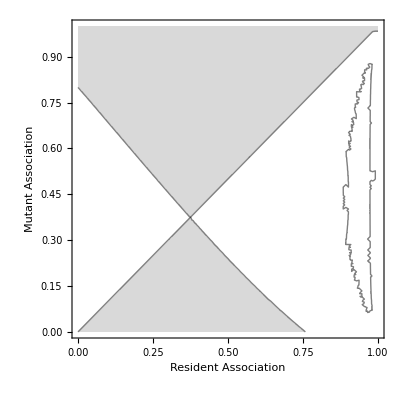

```mathematica
(*Contour plot of mutant trait values (Rm>1)*)
param3={cm,d,ω,λ,α, ζ,ξ, ψ, ra,rb, k,μa,μb,κ,β,χ, δ}//.{cm->cm, d->0, ω->10,λ->10,α->0,ζ->5, ξ->1,ψ-> 20, ra->2.2,rb->2.1, k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,χ->0.001, δ->.9};
param4={c,d,ω,λ,α, ζ,ξ, ψ, ra,rb, k,μa,μb,κ,β,χ, δ,astart,bstart,abstart, aOstart, bOstart}//.{c->c,d->0, ω->10,λ->10,α->0,ζ->5, ξ->1,ψ-> 20, ra->2.2,rb->2.1, k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,χ->0.001, δ->.9,astart->1,bstart->1,abstart->1, aOstart->1, bOstart->1};

ContourPlot[RmfunA@@param3/.NSolution@@param4/.t->500,{c,0,1},{cm,0,1},Contours->{1},ContourShading->{LightGray,White},FrameTicksStyle->Directive[FontFamily->"Helvetica", 12],FrameLabel->{Style["Resident Association ", Bold, 18], Style[ "Mutant Association", Bold, 18]},LabelStyle->Directive["Helvetica"]]
```

```mathematica
Invasion of Cooperation in B
```

B Cooperation in Invasion of

```mathematica
(*When species A evolves*) 
FmB=({{Subscript[F, B], Subscript[P, B], 1}, {0, 0, 0}, {0, 0, 0}}); (*reproduction*)
VmB=({{Subscript[β, B] X, 0, 0}, {-Subscript[β, B] X, Subscript[M, BA], -Subscript[A, B] X2}, {0, -Subscript[PR, B], Subscript[A, B] X2+1}}); (*transition between states*)

(* checking that next gen approach is valid *)
Eigenvalues[-VmB]
Inverse[VmB]

FmBVmB=FmB.Inverse[VmB]//MatrixForm
FmVmB=FmB-VmB//MatrixForm
```

{1/2 (-1-X2 A_B-M_BA-√((1+X2 A_B+M_BA)^2-4 (M_BA+X2 A_B M_BA-X2 A_B PR_B))),1/2 (-1-X2 A_B-M_BA+√((1+X2 A_B+M_BA)^2-4 (M_BA+X2 A_B M_BA-X2 A_B PR_B))),-X β_B}

{{(M_BA+X2 A_B M_BA-X2 A_B PR_B)/(X M_BA β_B+X X2 A_B M_BA β_B-X X2 A_B PR_B β_B),0,0},{(X β_B+X X2 A_B β_B)/(X M_BA β_B+X X2 A_B M_BA β_B-X X2 A_B PR_B β_B),(X β_B+X X2 A_B β_B)/(X M_BA β_B+X X2 A_B M_BA β_B-X X2 A_B PR_B β_B),(X X2 A_B β_B)/(X M_BA β_B+X X2 A_B M_BA β_B-X X2 A_B PR_B β_B)},{(X PR_B β_B)/(X M_BA β_B+X X2 A_B M_BA β_B-X X2 A_B PR_B β_B),(X PR_B β_B)/(X M_BA β_B+X X2 A_B M_BA β_B-X X2 A_B PR_B β_B),(X M_BA β_B)/(X M_BA β_B+X X2 A_B M_BA β_B-X X2 A_B PR_B β_B)}}

((F_B (M_BA+X2 A_B M_BA-X2 A_B PR_B))/(X M_BA β_B+X X2 A_B M_BA β_B-X X2 A_B PR_B β_B)+(X PR_B β_B)/(X M_BA β_B+X X2 A_B M_BA β_B-X X2 A_B PR_B β_B)+(P_B (X β_B+X X2 A_B β_B))/(X M_BA β_B+X X2 A_B M_BA β_B-X X2 A_B PR_B β_B) | (X PR_B β_B)/(X M_BA β_B+X X2 A_B M_BA β_B-X X2 A_B PR_B β_B)+(P_B (X β_B+X X2 A_B β_B))/(X M_BA β_B+X X2 A_B M_BA β_B-X X2 A_B PR_B β_B) | (X M_BA β_B)/(X M_BA β_B+X X2 A_B M_BA β_B-X X2 A_B PR_B β_B)+(X X2 A_B P_B β_B)/(X M_BA β_B+X X2 A_B M_BA β_B-X X2 A_B PR_B β_B)
0 | 0 | 0
0 | 0 | 0)

(F_B-X β_B | P_B | 1
X β_B | -M_BA | X2 A_B
0 | PR_B | -1-X2 A_B)

```mathematica
(*We are looking for the dominant eigenvalue Rm of the per-generation transition matrix FmVm*)
EmB=Eigensystem[FmB.Inverse[VmB]]
RmB=FullSimplify[EmB[[1,3]]]


emB=Eigensystem[FmB-VmB];
rmB=FullSimplify[emB[[1,2]]];
```

{{0,0,(F_B M_BA+X2 A_B F_B M_BA-X2 A_B F_B PR_B+X P_B β_B+X X2 A_B P_B β_B+X PR_B β_B)/(X (M_BA+X2 A_B M_BA-X2 A_B PR_B) β_B)},{{-(X (M_BA+X2 A_B P_B) β_B)/(F_B M_BA+X2 A_B F_B M_BA-X2 A_B F_B PR_B+X P_B β_B+X X2 A_B P_B β_B+X PR_B β_B),0,1},{-(X (P_B+X2 A_B P_B+PR_B) β_B)/(F_B M_BA+X2 A_B F_B M_BA-X2 A_B F_B PR_B+X P_B β_B+X X2 A_B P_B β_B+X PR_B β_B),1,0},{1,0,0}}}

(P_B+X2 A_B P_B+PR_B)/(M_BA+X2 A_B M_BA-X2 A_B PR_B)+F_B/(X β_B)

```mathematica
(*invasion fitness of the cooperation mutant in species B *)
dm=.
Subscript[F, B]=((rb(1-dm)((1-k(a[t]+ab[t]+b[t]+aO[t] +bO[t]))))-μb);
Subscript[P, B]=( μa + (1-ξ c)δ);
Subscript[M, BA]=(μa +μb + (1-ξ c)δ);
Subscript[β, B]=(1+ζ c)β ;
Subscript[A, B]= (1+ψ c )(1+λ dm)χ;
Subscript[PR, B]=(1+κ)(1-dm)rb((1-k(a[t]+ab[t]+b[t]+aO[t]+bO[t])));
Subscript[Rm, B]=(Subscript[P, B]+aO[t] Subscript[A, B] Subscript[P, B]+Subscript[PR, B])/(Subscript[M, BA]+aO[t] Subscript[A, B] Subscript[M, BA]-aO[t] Subscript[A, B] Subscript[PR, B])+Subscript[F, B]/(a[t] Subscript[β, B])
```

(-μb+(1-dm) rb (1-k (a[t]+ab[t]+aO[t]+b[t]+bO[t])))/(β (1+c ζ) a[t])+(μa+δ (1-c ξ)+(1+dm λ) (μa+δ (1-c ξ)) χ (1+c ψ) aO[t]+(1-dm) rb (1+κ) (1-k (a[t]+ab[t]+aO[t]+b[t]+bO[t])))/(μa+μb+δ (1-c ξ)+(1+dm λ) (μa+μb+δ (1-c ξ)) χ (1+c ψ) aO[t]-(1-dm) rb (1+κ) (1+dm λ) χ (1+c ψ) aO[t] (1-k (a[t]+ab[t]+aO[t]+b[t]+bO[t])))

```mathematica
(-μb+(1-dm) rb (1-k (a[t]+ab[t]+aO[t]+b[t]+bO[t])))/(β (1+c ζ) a[t])+(μa+δ (1-c ξ)+χ (μa+δ (1-c ξ)) (1+c ψ) aO[t]+(1-dm) rb (1+κ) (1-k (a[t]+ab[t]+aO[t]+b[t]+bO[t])))/(μa+μb+δ (1-c ξ)+χ (μa+μb+δ (1-c ξ)) (1+c ψ) aO[t]-(1-dm) rb χ (1+κ) (1+c ψ) aO[t] (1-k (a[t]+ab[t]+aO[t]+b[t]+bO[t])))
```

(-μb+(1-dm) rb (1-k (a[t]+ab[t]+aO[t]+b[t]+bO[t])))/(β (1+c ζ) a[t])+(μa+δ (1-c ξ)+(μa+δ (1-c ξ)) χ (1+c ψ) aO[t]+(1-dm) rb (1+κ) (1-k (a[t]+ab[t]+aO[t]+b[t]+bO[t])))/(μa+μb+δ (1-c ξ)+(μa+μb+δ (1-c ξ)) χ (1+c ψ) aO[t]-(1-dm) rb (1+κ) χ (1+c ψ) aO[t] (1-k (a[t]+ab[t]+aO[t]+b[t]+bO[t])))

```mathematica
(*Write invasion fitness in terms of parameter values *)

RmfunB[c_,dm_,ω_,λ_,α_, ζ_,ξ_, ψ_,ra_,rb_, k_, μa_, μb_,  κ_, β_,χ_, δ_]:=Evaluate[Subscript[Rm, B]]
gradRmfunB[c_,dm_,ω_,λ_,α_, ζ_,ξ_, ψ_,ra_,rb_, k_, μa_, μb_,  κ_, β_,χ_, δ_]:=Evaluate[D[Subscript[Rm, B],dm]/.dm->d]
ngValiditynegB[c_,dm_,ω_,λ_,α_, ζ_,ξ_, ψ_,ra_,rb_, k_, μa_, μb_,  κ_, β_,χ_, δ_]:=Evaluate[(1+aO[t] Subscript[A, B]) Subscript[M, BA]-aO[t] Subscript[A, B] Subscript[PR, B]]
ngValidityinverseB[c_,dm_,ω_,λ_,α_, ζ_,ξ_, ψ_,ra_,rb_, k_, μa_, μb_,  κ_, β_,χ_, δ_]:=Evaluate[1/2 (-1-aO[t] Subscript[A, B]-Subscript[M, BA]+√((1+aO[t] Subscript[A, B]-Subscript[M, BA])^2+4 aO[t] Subscript[A, B] Subscript[PR, B]))]
```

```mathematica
(*Confirm that neutral mutant (dm=d) won't evolve (Rm=1) *)
d=.;
dm=.;
param5={c,dm,ω,λ,α, ζ,ξ, ψ, ra,rb, k,μa,μb,κ,β,χ, δ}//.{c->0, dm->.5, ω->10,λ->10,α->0,ζ->5, ξ->1,ψ-> 20, ra->2.2,rb->2.1, k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,χ->0.001, δ->.9};;
param6={c,d,ω,λ,α, ζ,ξ, ψ, ra,rb, k,μa,μb,κ,β,χ, δ,astart,bstart,abstart, aOstart, bOstart}//.{c->0, d->.5, ω->10,λ->10,α->0,ζ->5, ξ->1,ψ-> 20, ra->2.2,rb->2.1, k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,χ->0.001, δ->.9,astart->1,bstart->1,abstart->1, aOstart->1, bOstart->1};
RmfunB@@param5/.NSolution@@param6/.t->500
ngValiditynegB@@param5/.NSolution@@param6/.t->500
ngValidityinverseB@@param5/.NSolution@@param6/.t->500
```

{1.}

{2.43816}

{-0.658032}

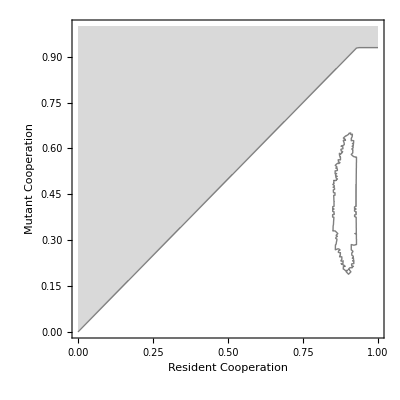

```mathematica
(*Contour plot of mutant trait values (Rm>1) before stickiness evolves (c=.2)*)
param7={c,dm,ω, λ,α,ζ,ξ, ψ, ra,rb, k,μa,μb,κ,β,χ, δ}//.{c->0, dm->dm, ω->10,λ->10,α->0,ζ->5, ξ->1,ψ-> 20, ra->2.2,rb->2.1, k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,χ->0.001, δ->.9};
param8={c,d,ω,λ,α, ζ,ξ, ψ, ra,rb, k,μa,μb,κ,β,χ, δ,astart,bstart,abstart, aOstart, bOstart}//.{c->0, d->d, ω->10,λ->10,α->0,ζ->5, ξ->1,ψ-> 20, ra->2.2,rb->2.1, k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,χ->0.001, δ->.9,astart->1,bstart->1,abstart->1, aOstart->1, bOstart->1};

ContourPlot[RmfunB@@param7/.NSolution@@param8/.t->500,{d,0,1},{dm,0,1},Contours->{1},ContourShading->{LightGray,White},FrameTicksStyle->Directive[FontFamily->"Helvetica", 12],FrameLabel->{Style["Resident Cooperation ", Bold, 18], Style[ "Mutant Cooperation", Bold, 18]},LabelStyle->Directive["Helvetica"]]
```

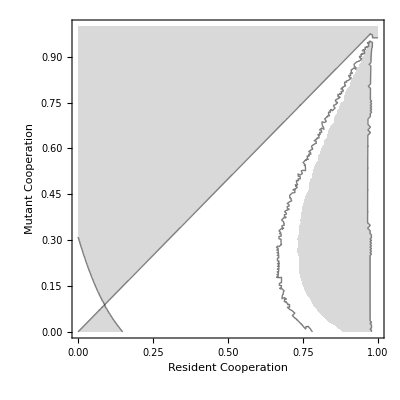

```mathematica
(*Contour plot of mutant trait values (Rm>1) after stickiness evolves (c=0)*)
param9={c,dm,ω,λ,α, ζ,ξ, ψ, ra,rb, k,μa,μb,κ,β,χ, δ}//.{c->.4, dm->dm, ω->10,λ->10,α->0,ζ->5, ξ->1,ψ-> 20, ra->2.2,rb->2.1, k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,χ->0.001, δ->.9};
param10={c,d,ω,λ,α, ζ,ξ, ψ, ra,rb, k,μa,μb,κ,β,χ, δ,astart,bstart,abstart, aOstart, bOstart}//.{c->.4, d->d, ω->10,λ->10,α->0,ζ->5, ξ->1,ψ-> 20, ra->2.2,rb->2.1, k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,χ->0.001, δ->.9,astart->1,bstart->1,abstart->1, aOstart->1, bOstart->1};

ContourPlot[RmfunB@@param9/.NSolution@@param10/.t->500,{d,0,1},{dm,0,1},Contours->{1},ContourShading->{LightGray,White},FrameTicksStyle->Directive[FontFamily->"Helvetica", 12],FrameLabel->{Style["Resident Cooperation ", Bold, 18], Style[ "Mutant Cooperation", Bold, 18]},LabelStyle->Directive["Helvetica"]]
```

```mathematica
(*Pairwise invasibility plot looking at coevolution*)
gradRmfunA[cm_,d_,ω_, λ_,α_,ζ_,ξ_, ψ_,ra_,rb_, k_, μa_, μb_,  κ_, β_,χ_, δ_]:=Evaluate[D[Subscript[Rm, A],cm]/.cm->c]
gradRmfunB[c_,dm_,ω_, λ_,α_,ζ_,ξ_, ψ_,ra_,rb_, k_, μa_, μb_,  κ_, β_,χ_, δ_]:=Evaluate[D[Subscript[Rm, B],dm]/.dm->d]
```

```mathematica
R01=ContourPlot[R0[p/20,py/20,Fs,Fy,κ,b,β,m,δs,δy,a,α,nh,ϕ,τ],{p,1,19},{py,1,19},PlotRange->{{1,19},{1,19}},PlotPoints->80,Contours->{1},ContourShading->{Black,None},Frame->None];
```

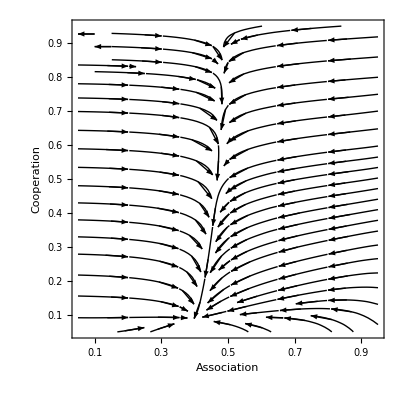

```mathematica
(*Coevolution*)
param={c,d,ω,λ,α, ζ,ξ, ψ, ra,rb, k,μa,μb,κ,β,χ, δ}//.{c->c, d->d, ω->10,λ->10,α->0,ζ->5, ξ->1,ψ-> 20, ra->2.2,rb->2.1, k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,χ->0.001, δ->.9};
paramEpid={c,d,ω,λ,α, ζ,ξ, ψ, ra,rb, k,μa,μb,κ,β,χ, δ, astart,bstart,abstart, aOstart, bOstart}//.{c->c, d->d, ω->10,λ->10,α->0,ζ->5, ξ->1,ψ-> 20, ra->2.2,rb->2.1, k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,χ->0.001, δ->.9,astart->1,bstart->1,abstart->1, aOstart->1, bOstart->1};


data=Table[{First [gradRmfunA@@param/.NSolution@@paramEpid/.t->500],First[gradRmfunB@@param/.NSolution@@paramEpid/.t->500]},{c,0.05,0.95,0.05},{d,0.05,0.95,0.05}];
gradPlot=ListStreamPlot[data,PlotTheme->"Monochrome",StreamPoints->50,StreamScale->{Large,All,0.04},PlotRange->All,Frame->True,ImageMargins->1,StreamStyle->"Arrow",FrameTicks->{{Table[{i,i*0.1/2},{i,2,18,2}],None},{Table[{i,i*0.1/2},{i,2,18,2}], None}},FrameLabel->{Style["Association", Bold,Gray, 18], Style[ "Cooperation", Bold,Gray, 18]},LabelStyle->Directive["Helvetica"], FrameTicksStyle->Directive[Black,10],AxesStyle->LightGray]
```

```mathematica
(*Potentially better code for pairwise plot*)
paramA={c,d,ω,λ,α, ζ,ξ, ψ, ra,rb, k,μa,μb,κ,β,χ, δ}//.{c->c, d->d, ω->10,λ->10,α->0,ζ->5, ξ->1,ψ-> 20, ra->2.2,rb->2.1, k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,χ->0.001, δ->.9};
paramB={c,d,ω,λ,α, ζ,ξ, ψ, ra,rb, k,μa,μb,κ,β,χ, δ}//.{c->c, d->d, ω->10,λ->10,α->0,ζ->5, ξ->1,ψ-> 20, ra->2.2,rb->2.1, k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,χ->0.001, δ->.9};
paramNum={c,d,ω,λ,α, ζ,ξ, ψ, ra,rb, k,μa,μb,κ,β,χ, δ, astart,bstart,abstart, aOstart, bOstart}//.{c->c, d->d, ω->10,λ->10,α->0,ζ->5, ξ->1,ψ-> 20, ra->2.2,rb->2.1, k->0.01,μa->1.1,μb->1.1,κ->100,β->0.01,χ->0.001, δ->.9,astart->1,bstart->1,abstart->1, aOstart->1, bOstart->1};
data=Table[{First [gradRmfunA@@paramA/.NSolution@@paramNum/.t->500],First[gradRmfunB@@paramB/.NSolution@@paramNum/.t->500]},{c,0.05,0.95,0.05},{d,0.05,0.95,0.05}];
gradPlot=ListStreamPlot[data,PlotTheme->"Monochrome",StreamPoints->50,StreamScale->{Large,All,0.04},PlotRange->All,Frame->True,ImageMargins->1,StreamStyle->"Arrow",FrameTicks->{{Table[{i,i*0.1/2},{i,2,18,2}],None},{Table[{i,i*0.1/2},{i,2,18,2}], None}},FrameLabel->{Style["Association", Bold,Gray, 18], Style[ "Cooperation", Bold,Gray, 18]},LabelStyle->Directive["Helvetica"], FrameTicksStyle->Directive[Black,10],AxesStyle->LightGray]
```

-Graphics-